```mathematica
Needs["NDSolve`FEM`"];
ClearAll[ sol,kappa,T0,Ptot,Pbkg,A,x,y,z,x0,y0,z0,sy,sz,Wrad,Rrad, Lstick, Hstick, Wstick, NormIntegral,powerDensity3DFunc, powerDensity3D, copperCylinderRegion, copperStickRegion, copperRegion, meshRegion];
```

```mathematica
$Assumptions=Lstick∈Reals&&Lstick>0&&Wstick∈Reals&&Wstick>0 &&Wrad∈Reals&&Wrad>0 && Hstick∈Reals&&Hstick>0 &&x0∈Reals&&y0∈Reals&& z0∈Reals&&Rrad∈Reals&&Rrad>0;
```

```mathematica
powerDensity3DFunc[x_,y_,z_]:= Piecewise[{{Exp[- ((z-z0)^2/(2*sz^2)+(y-y0)^2/(2*sy^2))],z>Lstick}},0];
(*powerDensity3DFunc[r_,θ_,z_]:=Piecewise[{{1.0,z≥z0}},0];*)
```

```mathematica
NormIntegral=Integrate[powerDensity3DFunc[x,y,z],{x,x0-Wrad/2,x0+Wrad/2},{y,y0-Rrad,y0+Rrad},{z,Lstick,Lstick+2*Rrad}]
```

-π sy sz Wrad Erf[Rrad/(√2 sy)] (Erf[(Lstick-z0)/(√2 sz)]-Erf[(Lstick+2 Rrad-z0)/(√2 sz)])

```mathematica
kappa=0.00385;T0=50.0; Ptot=0.010; minPower=0.0000001;
Wrad=0.14;(* Lzrad=1;*) Rrad=1.5;
Lstick=100;Hstick=2;Wstick=1;
x0=0;y0=0; z0=Lstick+Rrad;sy=0.1;sz=0.1;
```

```mathematica
NormIntegral
```

0.00879646

```mathematica
powerDensity3D[x_,y_,z_]:= Piecewise[{{Ptot/NormIntegral*powerDensity3DFunc[x,y,z], powerDensity3DFunc[x,y,z]>minPower}}, 0];
```

```mathematica
NIntegrate[powerDensity3D[x,y,z],{x,x0-Wrad/2,x0+Wrad/2},{y,y0-Rrad,y0+Rrad},{z,Lstick,Lstick+2*Rrad}]
```

0.01

```mathematica
Ptot/NormIntegral
```

1.13682

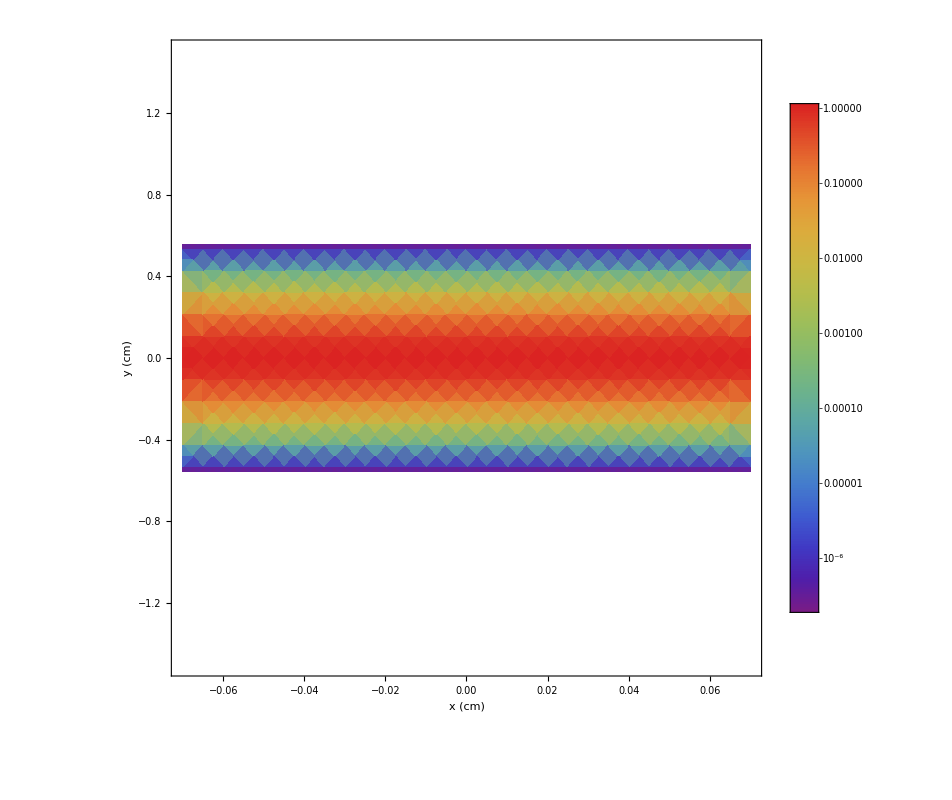

```mathematica
DensityPlot[powerDensity3D[x,y,z0],{x,x0-Wrad/2,x0+Wrad/2},{y,y0-Rrad,y0+Rrad},ColorFunction->{"Rainbow"},PlotRange->Full,PlotLegends->Automatic, ScalingFunctions->{Identity,Identity,"Log"},ImageSize->{800,800},FrameLabel->{"x (cm)", "y (cm)", "ΔE/ΔV (KW/SuperscriptBox[cm, 3] )"} , LabelStyle->{22,GrayLevel[0],Italic},AspectRatio->1]
```

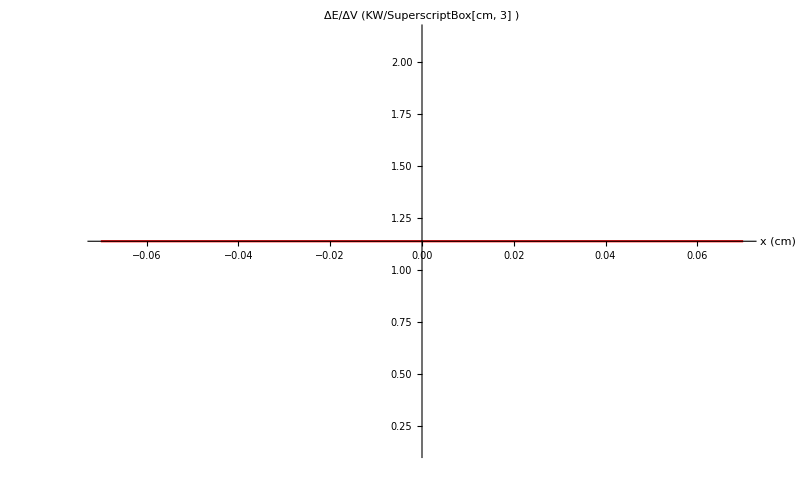

```mathematica
Plot[powerDensity3D[x,0,z0],{x,x0-Wrad/2,x0+Wrad/2}, AxesLabel->{"x (cm)", "ΔE/ΔV (KW/SuperscriptBox[cm, 3] )"} ,LabelStyle->{22,GrayLevel[0],Italic},AspectRatio->Full,ImageSize->{800,500},PlotRange->Full, PlotStyle->{Red,Thickness[0.002]}]
```

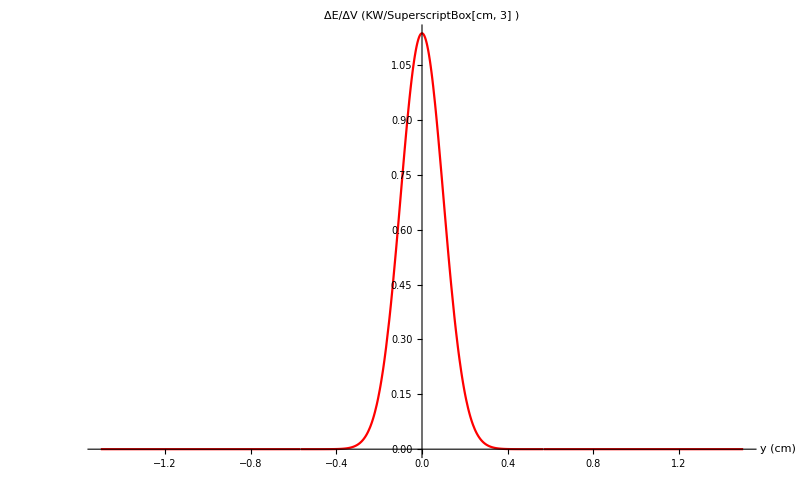

```mathematica
Plot[powerDensity3D[0,y,z0],{y,y0-Rrad,y0+Rrad}, AxesLabel->{"y (cm)", "ΔE/ΔV (KW/SuperscriptBox[cm, 3] )"} ,LabelStyle->{22,GrayLevel[0],Italic},AspectRatio->Full,ImageSize->{800,500},PlotRange->Full, PlotStyle->{Red,Thickness[0.002]}]
```

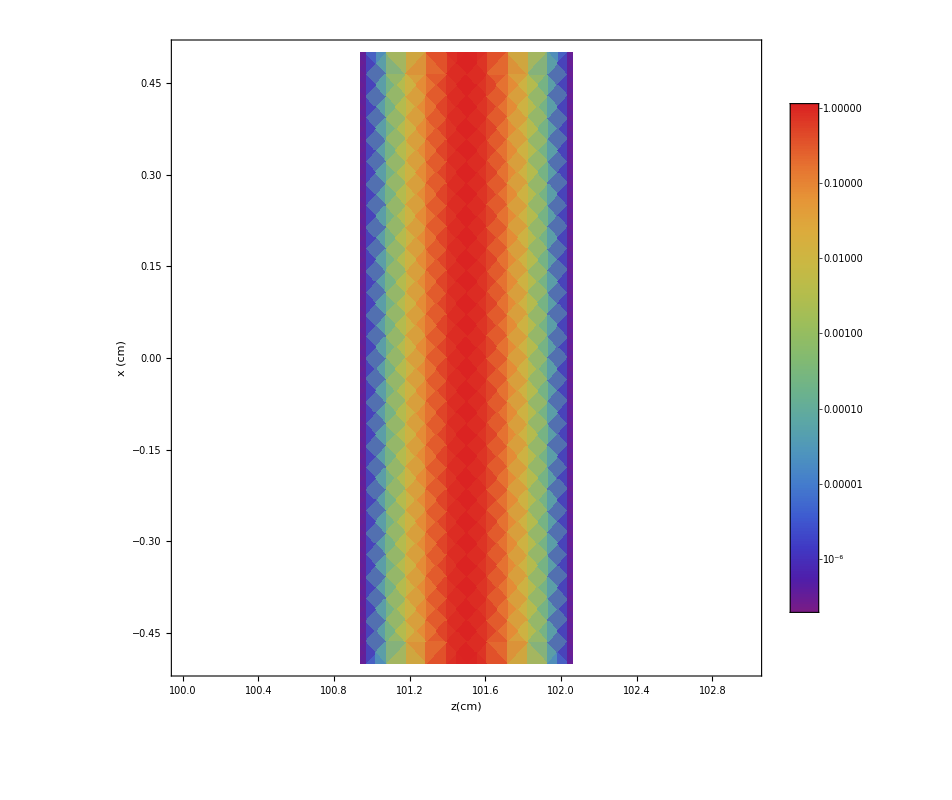

```mathematica
DensityPlot[powerDensity3D[x,y0,z],{z,Lstick-0*Rrad,Lstick+2*Rrad},{x,x0-Wstick/2,x0+Wstick/2},ColorFunction->"Rainbow",PlotRange->Full,PlotLegends->Automatic,ScalingFunctions->{Identity,Identity,"Log"},ImageSize->{800,800},FrameLabel->{"z(cm)", "x (cm)", "ΔE/ΔV (KW/SuperscriptBox[cm, 3] )"} , LabelStyle->{22,GrayLevel[0],Italic},AspectRatio->1]
```

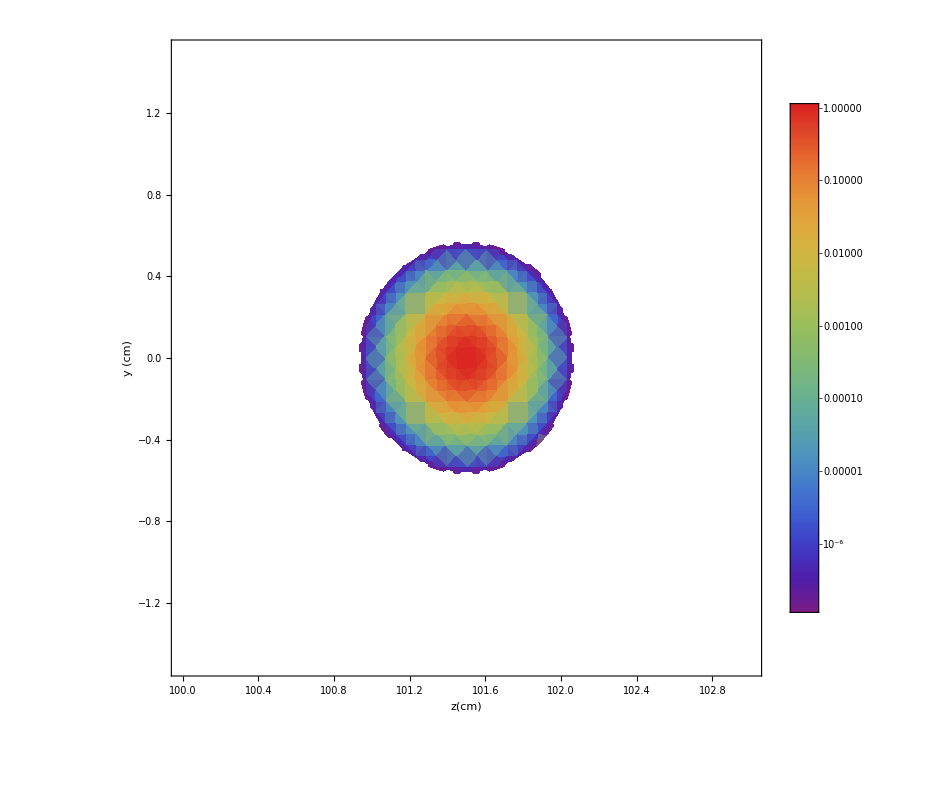

```mathematica
DensityPlot[powerDensity3D[0,y,z],{z,Lstick,Lstick+2*Rrad},{y,y0-Rrad,x0+Rrad},ColorFunction->"Rainbow",PlotRange->Full,PlotLegends->Automatic,ScalingFunctions->{Identity,Identity,"Log"},ImageSize->{800,800},FrameLabel->{"z(cm)", "y (cm)", "ΔE/ΔV (KW/SuperscriptBox[cm, 3] )"} , LabelStyle->{22,GrayLevel[0],Italic},AspectRatio->1]
```

```mathematica
copperSquareRegion=Cuboid[{x0-Wrad/2,y0-Rrad,Lstick},{x0+Wrad/2,y0+Rrad,Lstick+2*Rrad}];
(*RegionPlot3D[copperSquareRegion, Mesh->None]*)
```

```mathematica
copperStickRegion=Cuboid[{x0-Wstick/2,y0-Hstick/2,0},{x0+Wstick/2,y0+Hstick/2,Lstick}];
```

```mathematica
copperRegion = RegionUnion[copperSquareRegion,copperStickRegion];
(*copperRegion=copperStickRegion;*)
(*RegionPlot3D[copperRegion,Mesh->None]*)
```

```mathematica
boundaryMeshRegion=ToBoundaryMesh[copperRegion, MeshQualityGoal->"Maximal",(*"BoundaryMeshGenerator"->"Continuation",*) MaxBoundaryCellMeasure->{"Length"->0.03}];
(*boundaryMeshRegion["Wireframe"]*)
```

```mathematica
(*meshRegion=ToElementMesh[copperRegion, MeshQualityGoal->"Maximal",MaxCellMeasure->{"Volume"->0.3},  "BoundaryMeshGenerator"->"Continuation", MaxBoundaryCellMeasure->{"Length"->0.02}];*)
(*meshRegion["Wireframe"]*)
```

```mathematica
meshRegion=ToElementMesh[copperRegion,MeshQualityGoal->"Maximal",MaxBoundaryCellMeasure->{"Length"->0.03},MaxCellMeasure->{"Volume"->1}];
(*meshRegion["Wireframe"]*)
```

```mathematica
eqn=-Laplacian[u[x,y,z],{x,y,z}]==1/kappa*powerDensity3D[x,y,z]+ NeumannValue[0.0,{x,y,z}∈ boundaryMeshRegion] ;
```

```mathematica
(*eqn=-Laplacian[u[x,y,z],{x,y,z}]==1/kappa*powerDensity3D[x,y,z]+ NeumannValue[0.0,x==Wstick/2||x==-Wstick/2||y==Hstick/2||y==-Hstick/2||z==0||z==Lstick];*)
```

```mathematica
sol=NDSolveValue[{eqn,DirichletCondition[u[x,y,z]==T0,(z==0)]}, u,{x, y,z} ∈ meshRegion];
```

CompiledFunction::cfta: Argument {Boole[{-0.07,1.5,103.}∈ElementMesh[«1»]],Boole[{-0.07,1.16667,103.}∈ElementMesh[{{-0.277778,1.,99.7913},{-0.388889,1.,99.7913},{-0.277778,0.833333,100.},{-0.388889,0.833333,100.},{-0.277778,1.,99.4704},{-0.388889,1.,99.4704},{-0.277778,1.,99.1495},{-0.388889,1.,99.1495},«36»,{-0.277778,1.,93.053},{-0.388889,1.,93.053},{-0.277778,1.,92.7321},{-0.388889,1.,92.7321},{-0.277778,1.,92.4112},{-0.388889,1.,92.4112},«10294»},«9»,«1»,{PointElement[{{«1»},«50»}]}]],«48»,«11112»} at position 1 should be a rank 1 tensor of machine-size integers.

```mathematica
(*sol=NDSolveValue[{eqn,{u[x,y,0]==T0}}, u,{x,x0-Wstick/2,x0+Wstick/2},{y,y0-Hstick/2,y0+Hstick/2},{z,0,Lstick},MaxStepSize->0.001 , AccuracyGoal->10,PrecisionGoal->70] ;*)
```

```mathematica
(*sol=Import["/home/hovanes/Documents/Wolfram Mathematica/CPS_Temperature_With_Mathematica/t_radiator_solution_50CT0_100cmLong_1x2cm2Wide_1meshxp02bmesh.m"]*)
```

```mathematica
(*Export["/home/hovanes/Documents/Wolfram Mathematica/CPS_Temperature_With_Mathematica/t_radiator_solution_50CT0_100cmLong_1x2cm2Wide_1meshFromp03bmesh.m", sol]*)
```

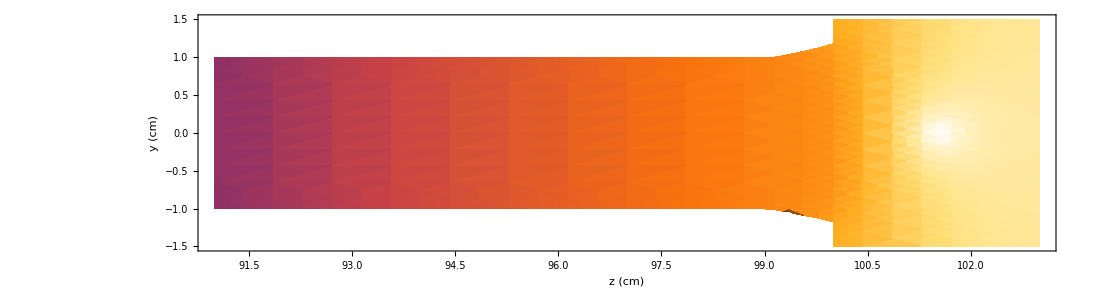

```mathematica
DensityPlot[sol[x0,y,z], {z,Lstick-6*Rrad,Lstick+2*Rrad},{y,y0-Rrad,y0+Rrad},ColorFunction->"SunsetColors",PlotLegends->Automatic,PlotRange->{160,200},ImageSize->{1100,400},FrameLabel->{"z (cm)", "y (cm)", "T (^oC)"} , LabelStyle->{22,GrayLevel[0],Italic},AspectRatio->0.27]
```

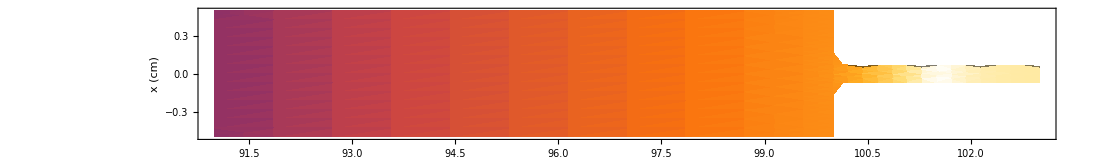

```mathematica
DensityPlot[sol[x,0,z], {z,Lstick-6*Rrad,Lstick+2*Rrad},{x,x0-Wstick/2,x0+Wstick/2},ColorFunction->"SunsetColors",PlotLegends->Automatic,PlotRange->{160,200},ImageSize->{1100,300},FrameLabel->{"z (cm)", "x (cm)", "T (^oC)"} , LabelStyle->{22,GrayLevel[0],Italic},AspectRatio->0.15]
```

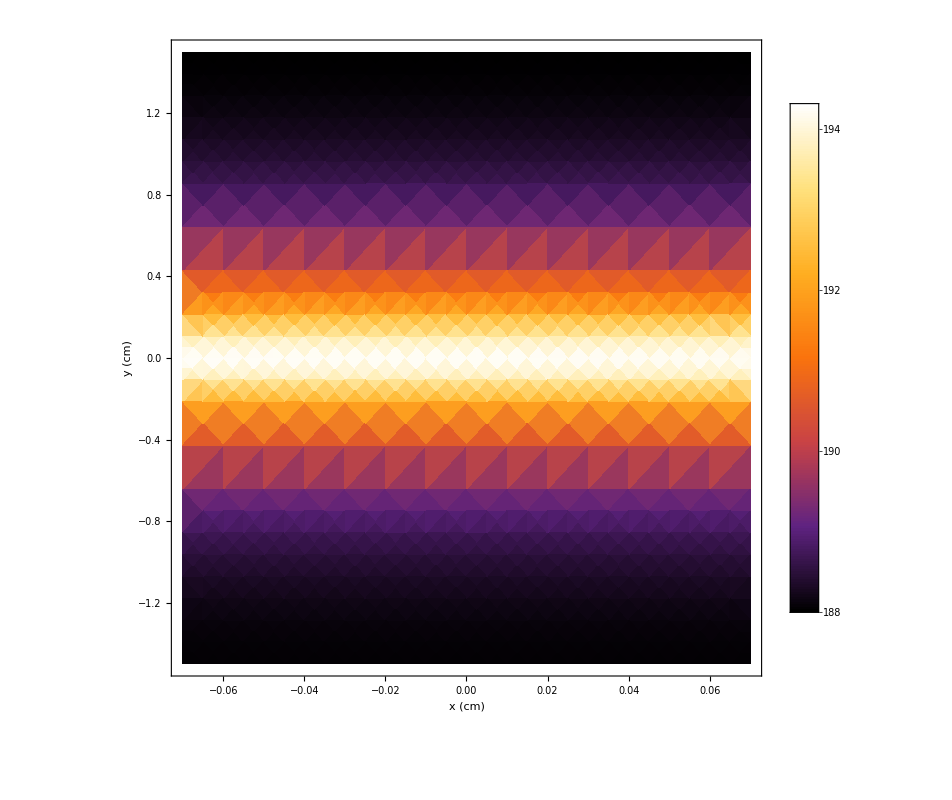

```mathematica
DensityPlot[sol[x,y,z0], {x,x0-Wrad/2,x0+Wrad/2},{y,y0-Rrad,y0+Rrad},ColorFunction->"SunsetColors",PlotLegends->Automatic,PlotRange->Full,ImageSize->{800,800},FrameLabel->{"x (cm)", "y (cm)", "T (^oC)"} , LabelStyle->{22,GrayLevel[0],Italic},AspectRatio->1]
```

```mathematica
SliceContourPlot3D[sol[x,y,z], "CenterPlanes",{x,x0-Wstick/2,x0+Wstick/2},{y,y0-Rrad,y0+Rrad},{z,0,Lstick+2*Rrad}, PlotTheme->"Detailed",PlotRange->Full,  ImageSize->{800,800},PlotLabel->"T (^oC)",AxesLabel->{ "x (cm)", "y (cm)","z (cm)"},LabelStyle->{22,GrayLevel[0],Italic}]
```

-Graphics3D-

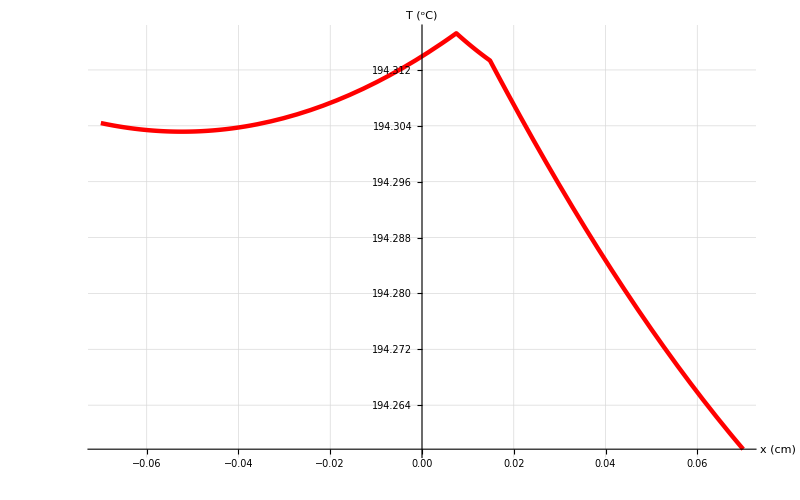

```mathematica
Plot[sol[x,y0,z0], {x,x0-Wrad/2,x0+Wrad/2},GridLines->Automatic,PlotRange->Full,AxesLabel->{"x (cm)", "T (^oC)"} ,LabelStyle->{22,GrayLevel[0],Italic},AspectRatio->Full,ImageSize->{800,500}, PlotStyle->{Red,Thickness[0.004]}]
```

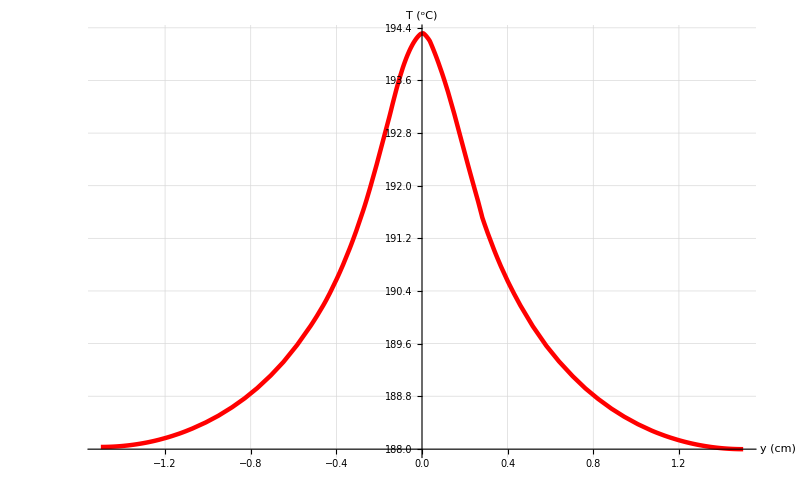

```mathematica
Plot[sol[x0,y,z0], {y,y0-Rrad,y0+Rrad},GridLines->Automatic,PlotRange->Full,AxesLabel->{"y (cm)", "T (^oC)"} ,LabelStyle->{22,GrayLevel[0],Italic},AspectRatio->Full,ImageSize->{800,500}, PlotStyle->{Red,Thickness[0.004]}]
```

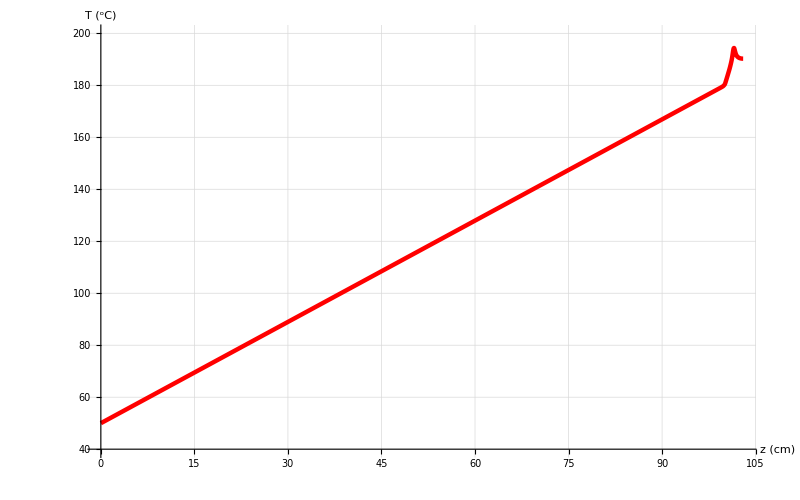

```mathematica
Plot[sol[x0,y0,z], {z,0,Lstick+2*Rrad},GridLines->Automatic,PlotRange->{40,200},AxesLabel->{"z (cm)", "T (^oC)"} ,LabelStyle->{22,GrayLevel[0],Italic},AspectRatio->Full,ImageSize->{800,500}, PlotStyle->{Red,Thickness[0.004]}]
```